```mathematica
g[x_]:=1/x
```

```mathematica
(g[x]-g[a])/(x-a)//Simplify//TraditionalForm
```

-1/(a x)

```mathematica
h[x_]:=(x+3)/(x+1)
```

```mathematica
(h[x]-h[1])/(x-1)//Simplify//TraditionalForm
```

-1/(x+1)

```mathematica
(h (h+3))/(h^2-3 h-4)
```

```mathematica
f[h]//Factor
f[3]
f[3+h]//Simplify
```

-(-4+h) (1+h)

4

4-3 h-h^2

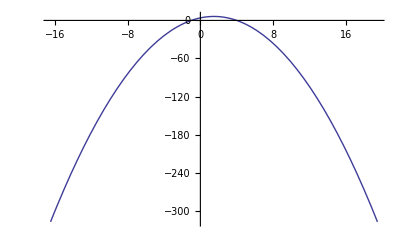

```mathematica
Plot[4+3 x-x^2,{x,-16.5,19.5}]
```

```mathematica
f[a]//TraditionalForm
```

-a^2+3 a+4

```mathematica
g[u_]:=Sqrt[u]+Sqrt[4-u]
```

```mathematica
Reduce[4-u>=0&&u≥0,u]
```

0≤u≤4

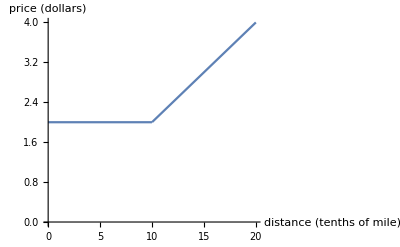

```mathematica
f[x_]:=Piecewise[{{2,x≤10},{2+.2(x-10),x>10}}]
Plot[f[x], {x, 0, 20},AxesOrigin->{0,0},AxesLabel->{"distance (tenths of mile)","price (dollars)"}]
```

```mathematica
Factor[x^2+3x+2]//TraditionalForm
```

(x+1) (x+2)

```mathematica
Reduce[x^2-5x>0,x]
```

x<0||x>5

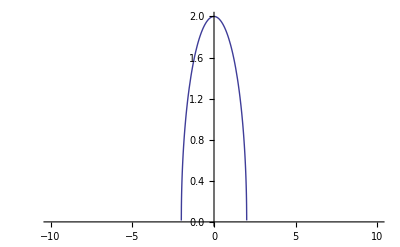

```mathematica
Plot[Sqrt[4-x^2], {x,-10,10}]
```

```mathematica
Reduce[2x+2y==20,y]
```

y==10-x

```mathematica
Reduce[x+2h+Pi x ==20,h]
```

h==10-1/2 (1+π) x

```mathematica
Simplify[1/2 Pi(x/2)^2]
```

(π x^2)/8

```mathematica
x(10-(1+Pi)/2 x)+Pi x^2/8
```

(π x^2)/8+x (10-1/2 (1+π) x)

```mathematica
x (12-2x) (20-2x)//Expand//TraditionalForm
```

4 x^3-64 x^2+240 x

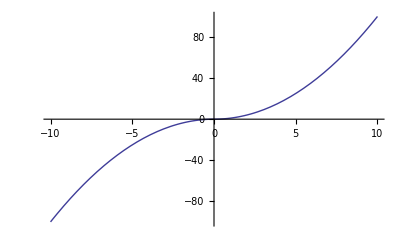

```mathematica
Plot[x Abs[x],{x,-10,10},AxesOrigin->{0,0}]
```

```mathematica
3/5 821//N
```

492.6

```mathematica
data:={{1990,11},{1992,26},{1994,60},{1996,160},{1998,340},{2000,650}}
```

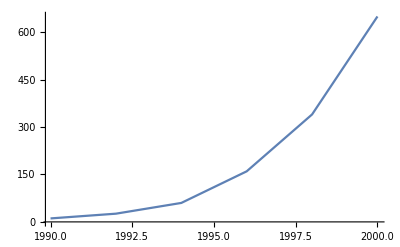

```mathematica
ListLinePlot[data]
```

```mathematica
x(12-2x)(20-2x)//Expand//TraditionalForm
```

4 x^3-64 x^2+240 x